# Problem 3.3

-Graphics-

```mathematica
ClearAll[H,pPhi,phi,psiS,Omega]

H[pPhi_,phi_,psiS_,Omega_]:=pPhi^2/2+Omega^2/Cos[psiS]*(Cos[psiS+phi]-Cos[psiS]+phi*Sin[psiS]);
```

```mathematica
psiSValue=Pi;
OmegaValue=1;
```

```mathematica
ContourPlot[Evaluate[H[pPhi,phi,psiSValue,OmegaValue]],{phi,-2 Pi,2 Pi},{pPhi,-3,3},Contours->30,ContourShading->True,ContourStyle->Thick,Frame->True,FrameLabel->{Style["ϕ",15],Style[Subscript["p","ϕ"],15]},PlotLabel->Row[{Subscript["ψ","s"]," = ",TraditionalForm[psiSValue]}],PlotPoints->80,MaxRecursion->2,AspectRatio->0.3]
```

-Graphics-

```mathematica
Manipulate[ContourPlot[Evaluate[H[pPhi,phi,psiS,1]],{phi,-2 Pi,2 Pi},{pPhi,-3,3},Contours->30,ContourShading->True,FrameLabel->{Style["ϕ",15],Style[Subscript["p","ϕ"],15]},PlotLabel->Row[{Subscript["ψ","s"]," = ",NumberForm[psiS,{4,2}]}],PlotPoints->80,MaxRecursion->2,AspectRatio->0.3],{{psiS,Pi,Subscript["ψ","s"]},Pi/2+0.05,3 Pi/2-0.05}]
```

```mathematica
ClearAll[energy,kModulus,u0,sigma0,z0,thetaExact,pExact,theta0Value,p0Value,eValue,kValue,periodValue];

(*Energy from initial conditions*)
energy[theta0_?NumericQ,p0_?NumericQ]:=p0^2/2-Cos[theta0];

(*Elliptic modulus k*)
kModulus[theta0_?NumericQ,p0_?NumericQ]:=Sqrt[(1+energy[theta0,p0])/2];

(*Initial elliptic amplitude*)
u0[theta0_?NumericQ,p0_?NumericQ]:=Module[{k},k=kModulus[theta0,p0];
ArcSin[Sin[theta0/2]/k]];

(*Initial direction of motion*)
sigma0[p0_?NumericQ]:=If[p0>=0,1,-1];

(*Initial Jacobi argument*)
z0[theta0_?NumericQ,p0_?NumericQ]:=Module[{k},k=kModulus[theta0,p0];
EllipticF[u0[theta0,p0],k^2]];
```

```mathematica
thetaExact[tau_?NumericQ,theta0_?NumericQ,p0_?NumericQ]:=Module[{k,z,sigma},k=kModulus[theta0,p0];
sigma=sigma0[p0];
z=z0[theta0,p0]+sigma tau;
2 ArcSin[k JacobiSN[z,k^2]]];
```

```mathematica
pExact[tau_?NumericQ,theta0_?NumericQ,p0_?NumericQ]:=Module[{k,z,sigma},k=kModulus[theta0,p0];
sigma=sigma0[p0];
z=z0[theta0,p0]+sigma tau;
2 sigma k JacobiCN[z,k^2]];
```

```mathematica
theta0Value=0.7;
p0Value=0.5;

eValue=energy[theta0Value,p0Value];
kValue=kModulus[theta0Value,p0Value];
periodValue=4 EllipticK[kValue^2];

N[{eValue,kValue,periodValue}]
```

{-0.639842,0.424357,6.59887}

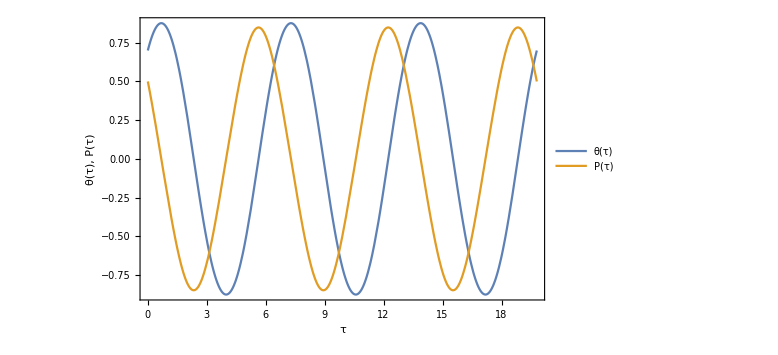

```mathematica
Plot[{thetaExact[tau,theta0Value,p0Value],pExact[tau,theta0Value,p0Value]},{tau,0,3 periodValue},Frame->True,FrameLabel->{Style["τ",14],Style["θ(τ), P(τ)",14]},PlotLegends->{"θ(τ)","P(τ)"},PlotRange->All,ImageSize->Large]
```

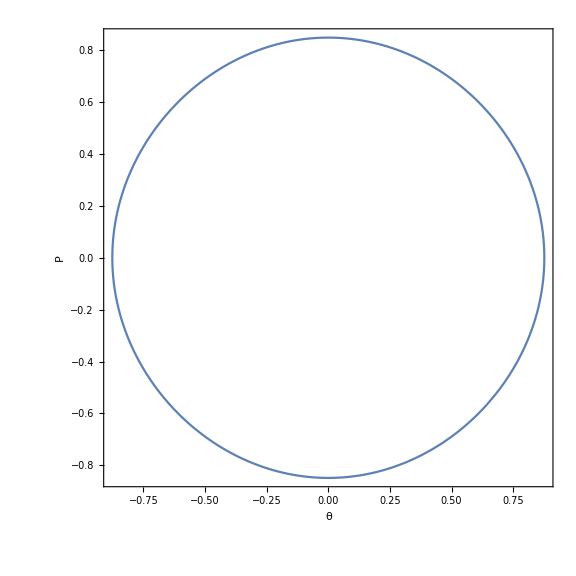

```mathematica
ParametricPlot[{thetaExact[tau,theta0Value,p0Value],pExact[tau,theta0Value,p0Value]},{tau,0,periodValue},Frame->True,FrameLabel->{Style["θ",14],Style["P",14]},PlotRange->All,AspectRatio->1,ImageSize->Large]
```

```mathematica
ClearAll[energy,kModulus,initialArgument,thetaExact,pExact];

(*Hamiltonian energy*)
energy[theta0_?NumericQ,p0_?NumericQ]:=p0^2/2-Cos[theta0];

(*Elliptic modulus k*)
kModulus[theta0_?NumericQ,p0_?NumericQ]:=Sqrt[(1+energy[theta0,p0])/2];

(*Initial argument of the Jacobi elliptic functions*)
initialArgument[theta0_?NumericQ,p0_?NumericQ]:=Module[{k,sn0,cn0,u0},k=kModulus[theta0,p0];
sn0=Clip[Sin[theta0/2]/k,{-1,1}];
cn0=Clip[p0/(2 k),{-1,1}];
(*Selects the correct quadrant using both theta0 and p0*)u0=ArcTan[cn0,sn0];
(*Mathematica uses k^2 as its elliptic parameter*)EllipticF[u0,k^2]];
```

```mathematica
thetaExact[tau_?NumericQ,theta0_?NumericQ,p0_?NumericQ]:=Module[{k,z0},k=kModulus[theta0,p0];
z0=initialArgument[theta0,p0];
2 ArcSin[k JacobiSN[z0+tau,k^2]]];

pExact[tau_?NumericQ,theta0_?NumericQ,p0_?NumericQ]:=Module[{k,z0},k=kModulus[theta0,p0];
z0=initialArgument[theta0,p0];
2 k JacobiCN[z0+tau,k^2]];
```

```mathematica
Manipulate[Module[{es,k,period,timePlot,phasePlot,separatrix},es=energy[theta0,p0];
Which[(*Exact stable fixed point*)Abs[es+1]<10^-10,Column[{Style["Stable fixed point: θ(τ) = 0 and P(τ) = 0",14],Graphics[{PointSize[0.025],Point[{0,0}]},Frame->True,FrameLabel->{"θ","P"},PlotRange->{{-Pi,Pi},{-2.2,2.2}},AspectRatio->1,ImageSize->Large]}],(*Librational motion*)-1<es<1,k=Sqrt[(1+es)/2];
period=4 EllipticK[k^2];
timePlot=Plot[{thetaExact[tau,theta0,p0],pExact[tau,theta0,p0]},{tau,0,nPeriods period},Frame->True,FrameLabel->{Style["τ",14],Style["θ(τ), P(τ)",14]},PlotLegends->{"θ(τ)","P(τ)"},PlotRange->All,ImageSize->Large];
separatrix=Plot[{2 Cos[theta/2],-2 Cos[theta/2]},{theta,-Pi,Pi},PlotStyle->{Directive[Gray,Dashed],Directive[Gray,Dashed]}];
phasePlot=Show[separatrix,ParametricPlot[{thetaExact[tau,theta0,p0],pExact[tau,theta0,p0]},{tau,0,period},PlotStyle->Thick],Graphics[{PointSize[0.022],Point[{theta0,p0}]}],Frame->True,FrameLabel->{Style["θ",14],Style["P",14]},PlotRange->{{-Pi,Pi},{-2.2,2.2}},AspectRatio->1,ImageSize->Large];
Column[{Grid[{{Style["Energy",Bold],NumberForm[es,{7,4}],Spacer[20],Style["Modulus k",Bold],NumberForm[k,{7,4}]},{Style["Period",Bold],NumberForm[period,{8,4}],Spacer[20],Style["Motion",Bold],"Libration"}}],timePlot,phasePlot}],(*Separatrix or rotational region*)True,Style[Column[{Row[{"The selected initial conditions give E = ",NumberForm[es,{7,4}],"."}],"The librational solution requires -1 < E < 1.",If[Abs[es-1]<10^-6,"The point is on the separatrix.","These initial conditions correspond to rotational motion."]}],Red,14]]],{{theta0,0.7,Subscript["θ","0"]},-Pi,Pi,0.01,Appearance->"Labeled"},{{p0,0.5,Subscript["P","0"]},-2.2,2.2,0.01,Appearance->"Labeled"},{{nPeriods,3,"number of periods"},1,10,1,Appearance->"Labeled"},ControlPlacement->Left,TrackedSymbols:>{theta0,p0,nPeriods},SaveDefinitions->True]
```

```mathematica
ClearAll[pendulumSolution];

pendulumSolution[theta0_?NumericQ,p0_?NumericQ,tau0_:0]:=Module[{energyValue,thetaWrapped,thetaShift,sigma,tolerance=10^-10,k,kr,kappa,sn0,cn0,u0,z0,crossingTime},(*Hamiltonian energy*)energyValue=p0^2/2-Cos[theta0];
(*Put the initial phase in[-Pi,Pi)*)thetaWrapped=Mod[theta0+Pi,2 Pi]-Pi;
(*Preserve the original winding number*)thetaShift=theta0-thetaWrapped;
sigma=If[p0>=0,1,-1];
Which[(* =========================================*)(*BOUNDED MOTION:-1<E<1*)(* =========================================*)energyValue<1-tolerance,k=Sqrt[(1+energyValue)/2];
sn0=Sin[thetaWrapped/2]/k;
cn0=p0/(2 k);
(*Correct elliptic amplitude quadrant*)u0=ArcTan[cn0,sn0];
(*Mathematica uses k^2 as its parameter*)z0=EllipticF[u0,k^2];
With[{kk=k,zz0=z0,shift=thetaShift,e=energyValue,tInitial=tau0},<|"Motion"->"Libration","Energy"->e,"Modulus"->kk,"Period"->4 EllipticK[kk^2],"Theta"->Function[{tau},shift+2 ArcSin[kk JacobiSN[zz0+tau-tInitial,kk^2]]],"Momentum"->Function[{tau},2 kk JacobiCN[zz0+tau-tInitial,kk^2]]|>],(* =========================================*)(*ROTATIONAL MOTION:E>1*)(* =========================================*)energyValue>1+tolerance,(*kappa>1 is the book's rotational k*)kappa=Sqrt[(energyValue+1)/2];
(*Reciprocal modulus,less than one*)kr=1/kappa;
z0=EllipticF[thetaWrapped/2,kr^2];
With[{kap=kappa,reciprocalK=kr,zz0=z0,direction=sigma,shift=thetaShift,e=energyValue,tInitial=tau0},<|"Motion"->"Rotation","Energy"->e,"Modulus"->reciprocalK,"Period"->2 EllipticK[reciprocalK^2]/kap,"Theta"->Function[{tau},shift+2 JacobiAmplitude[zz0+direction kap (tau-tInitial),reciprocalK^2]],"Momentum"->Function[{tau},2 direction kap JacobiDN[zz0+direction kap (tau-tInitial),reciprocalK^2]]|>],(* =========================================*)(*SEPARATRIX:E=1*)(* =========================================*)True,If[Abs[p0]<tolerance&&Abs[Abs[thetaWrapped]-Pi]<10^-8,(*Unstable fixed point*)With[{thetaFixed=theta0,e=energyValue},<|"Motion"->"Unstable fixed point","Energy"->e,"Modulus"->1,"Period"->Infinity,"Theta"->Function[{tau},thetaFixed],"Momentum"->Function[{tau},0]|>],(*General separatrix trajectory*)crossingTime=tau0-sigma Log[Tan[(Pi+thetaWrapped)/4]];
With[{direction=sigma,tc=crossingTime,shift=thetaShift,e=energyValue},<|"Motion"->"Separatrix","Energy"->e,"Modulus"->1,"Period"->Infinity,"Theta"->Function[{tau},shift+4 ArcTan[Exp[direction (tau-tc)]]-Pi],"Momentum"->Function[{tau},2 direction Sech[tau-tc]]|>]]]];
```

```mathematica
Manipulate[Module[{solution,energyValue,motionType,characteristicTime,timeMaximum,timePlot,phasePlot,separatrixPlot},solution=pendulumSolution[theta0,p0];
energyValue=solution["Energy"];
motionType=solution["Motion"];
characteristicTime=If[NumericQ[solution["Period"]]&&solution["Period"]=!=Infinity,solution["Period"],10];
timeMaximum=nPeriods characteristicTime;
timePlot=Plot[{solution["Theta"][tau],solution["Momentum"][tau]},{tau,0,timeMaximum},Frame->True,FrameLabel->{Style["τ",14],Style["θ(τ), P(τ)",14]},PlotLegends->{"θ(τ)","P(τ)"},PlotRange->All,ImageSize->Large];
separatrixPlot=Plot[{2 Cos[theta/2],-2 Cos[theta/2]},{theta,-Pi,Pi},PlotStyle->{Directive[Gray,Dashed],Directive[Gray,Dashed]}];
phasePlot=Show[separatrixPlot,ParametricPlot[{Mod[solution["Theta"][tau]+Pi,2 Pi]-Pi,solution["Momentum"][tau]},{tau,0,timeMaximum},PlotStyle->Thick,PlotPoints->150],Graphics[{PointSize[0.022],Point[{Mod[theta0+Pi,2 Pi]-Pi,p0}]}],Frame->True,FrameLabel->{Style["θ",14],Style["P",14]},PlotRange->{{-Pi,Pi},{-3.5,3.5}},AspectRatio->1,ImageSize->Large];
Column[{Grid[{{Style["Energy",Bold],NumberForm[energyValue,{7,4}],Spacer[20],Style["Motion",Bold],motionType},{Style["Initial phase",Bold],NumberForm[theta0,{6,3}],Spacer[20],Style["Initial momentum",Bold],NumberForm[p0,{6,3}]},{Style["Period",Bold],If[solution["Period"]===Infinity,"∞",NumberForm[solution["Period"],{8,4}]],Spacer[20],Style["Modulus",Bold],NumberForm[solution["Modulus"],{7,4}]}}],timePlot,phasePlot}]],{{theta0,0.7,Subscript["θ","0"]},-Pi,Pi,0.01,Appearance->"Labeled"},{{p0,0.5,Subscript["P","0"]},-3,3,0.01,Appearance->"Labeled"},{{nPeriods,3,"number of periods"},1,10,1,Appearance->"Labeled"},ControlPlacement->Left,TrackedSymbols:>{theta0,p0,nPeriods},SaveDefinitions->True]
```